# VYA - Přednášky

## 7. Přednáška

### Operační zesilovač

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Rovn = {IR1 == IR3,
IR2 == IR4,
uPlus == R4 * IR4,
U1 - uPlus == R2 * IR2,
U2 - uMinus == R1 * IR1,
uMinus - uOut == R3 * IR3,
uOut == A * (uPlus - uMinus)}

Neznam = {IR1, IR2, IR3, IR4, uPlus, uMinus, uOut};
Symb = Union[Cases[Rovn, _Symbol, {0, ∞}]]
Length /@ {Rovn, Neznam, Symb}

Res = Solve[Rovn, Neznam][[1]]
uout = Simplify[Limit[uOut /. Res, A -> ∞] /. {R1 -> R, R2 -> R, R3 -> Au * R, R4 -> Au * R}]
```

{IR1==IR3,IR2==IR4,uPlus==IR4 R4,U1-uPlus==IR2 R2,U2-uMinus==IR1 R1,uMinus-uOut==IR3 R3,uOut==A (-uMinus+uPlus)}

{A,IR1,IR2,IR3,IR4,R1,R2,R3,R4,U1,U2,uMinus,uOut,uPlus}

{7,7,14}

{IR1→-(A R4 U1-R2 U2-A R2 U2-R4 U2-A R4 U2)/((R1+A R1+R3) (R2+R4)),IR2→U1/(R2+R4),IR3→-(A R4 U1-R2 U2-A R2 U2-R4 U2-A R4 U2)/((R1+A R1+R3) (R2+R4)),IR4→U1/(R2+R4),uPlus→(R4 U1)/(R2+R4),uMinus→-(-A R1 R4 U1-R2 R3 U2-R3 R4 U2)/((R1+A R1+R3) (R2+R4)),uOut→-((-A R1 R4 U1-A R3 R4 U1+A R2 R3 U2+A R3 R4 U2)/((R1+A R1+R3) (R2+R4)))}

Au (U1-U2)

```mathematica
Simplify[Limit[-U1/IR1 /. Res, A -> ∞] //. {R1 -> R, R2 -> R, R3 -> Au * R, R4 -> Au * R}] /. U2 -> 0
```

((1+Au) R)/Au

### Harmonický ustálený stav

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
n = 1;
Rovn = 0 == ∑_(i=0)^n Subscript[a, 1]*x^i
Solve[Rovn, x]
```

0==a_1+x a_1

{{x→-1}}

```mathematica
n = 2;
Rovn = 0 == ∑_(i=0)^n Subscript[a, 1]*x^i
Solve[Rovn, x]
```

0==a_1+x a_1+x^2 a_1

{{x→-(-1)^(1/3)},{x→(-1)^(2/3)}}

```mathematica
n = 3;
Rovn = 0 == ∑_(i=0)^n Subscript[a, 1]*x^i
Solve[Rovn, x]
```

0==a_1+x a_1+x^2 a_1+x^3 a_1

{{x→-1},{x→-ⅈ},{x→ⅈ}}

### Obvod HUS

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
UIn = 10 * Sin[314 t];
L = 0.033;
μF = 10^-6;
Cl = 4.7 μF;
R1 = 47;
R2 = 100;
```

{IL[t]+IR1[t]==ICl[t]+IR2[t],UOut[t]==100 IR2[t],ICl[t]==4.7×10^-6 UOut'[t],10 Sin[314 t]-UOut[t]==47 IR1[t],10 Sin[314 t]-UOut[t]==0.033 IL'[t]}

{ICl,IL,IR1,IR2,UOut}

{5,5}

{IL[0]==0,UOut[0]==0}

{ICl[t]==4.7×10^-6 UOut'[t],IL[0]==0,IL[t]+IR1[t]==ICl[t]+IR2[t],UOut[0]==0,10 Sin[314 t]-UOut[t]==47 IR1[t],10 Sin[314 t]-UOut[t]==0.033 IL'[t],UOut[t]==100 IR2[t]}

{ICl→InterpolatingFunction[…],IL→InterpolatingFunction[…],IR1→InterpolatingFunction[…],IR2→InterpolatingFunction[…],UOut→InterpolatingFunction[…]}

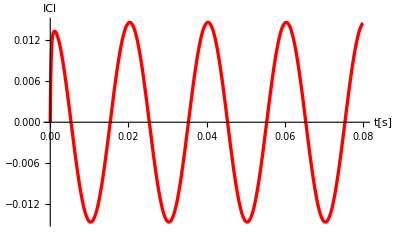
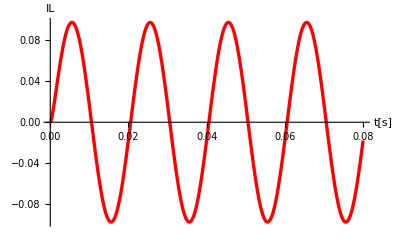
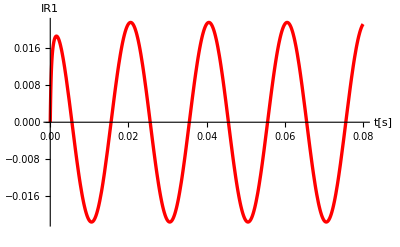
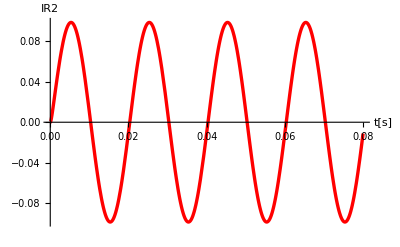
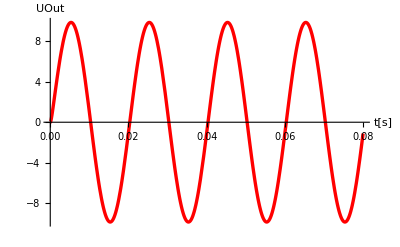

```mathematica
Rovn = {IR1[t] + IL[t] == ICl[t] + IR2[t],
UOut[t] == R2 * IR2[t],
ICl[t] == Cl * UOut'[t],
UIn - UOut[t] == R1 * IR1[t],
UIn - UOut[t] == L * IL'[t]
}
Nezname = Union[Cases[Rovn, a_Symbol[t] :> a, {0, ∞}]]
Length /@ {Rovn, Nezname}
PocPod = Union[Cases[Rovn, a_'[t] :> a[0] == 0, {0, ∞}]]
RovnPod = Union[Rovn, PocPod]
tMax = 0.08;
Res = NDSolve[RovnPod, Nezname, {t, 0, tMax}, StartingStepSize->10^-9][[1]]
Plot[#[t] /. Res, {t, 0, tMax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ Nezname
```

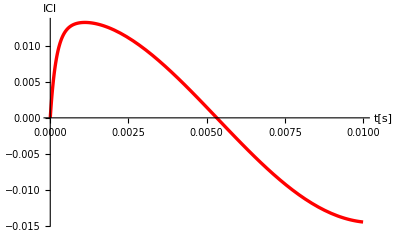
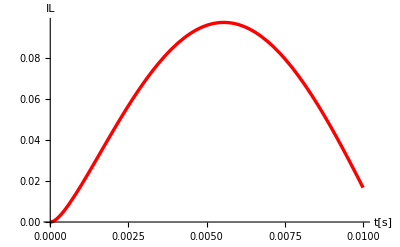
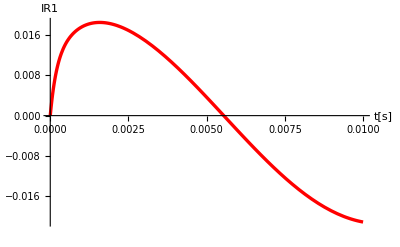
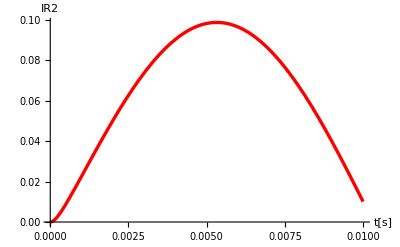
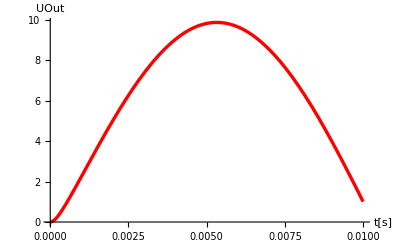

```mathematica
tMax = 0.01;
Res = NDSolve[RovnPod, Nezname, {t, 0, tMax}, StartingStepSize->10^-9][[1]];
Plot[#[t] /. Res, {t, 0, tMax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ Nezname
```

```mathematica
FullForm[ICl /. Res]
```